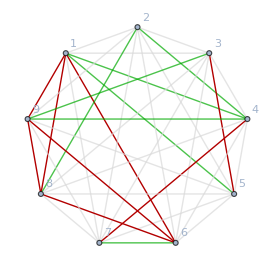
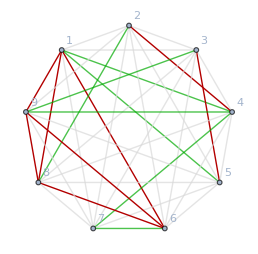
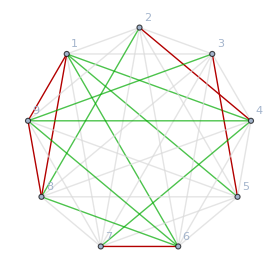
{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{1<->2<->{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},1<->3<->{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},1<->7<->{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},2<->6<->{-Graphics-,-Graphics-,-Graphics-,-Graphics-},2<->9<->{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},3<->4<->{-Graphics-},3<->6<->{-Graphics-},3<->8<->{-Graphics-},4<->5<->{-Graphics-},4<->6<->{-Graphics-,-Graphics-,-Graphics-,-Graphics-},4<->8<->{-Graphics-,-Graphics-,-Graphics-,-Graphics-},5<->6<->{-Graphics-},5<->8<->{-Graphics-},5<->9<->{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},7<->8<->{-Graphics-,-Graphics-,-Graphics-,-Graphics-},7<->9<->{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}}

```mathematica
With[{g=ReadGrof[45]},
{Map[Framed,FindB4CReduction[g]],Table[e<->ContractReduction[g,e],{e,CollectMPGEdges[g]}]}]
```